# Hints for a gravitational constant transition in Tully-Fisher data - G. Alestas, I. Antoniou and L. Perivolaropoulos - Figure 1, 2

## General Settings

### Setting the Environment

```mathematica
SetDirectory[NotebookDirectory[]]
Off[General::obspkg,First::nofirst,InterpolatingFunction::dmval,FindMinimum::lstol];
```

D:\Games\Dropbox\Research\tully-fisher-Geff\giorgos-math-files

### Importing Data

```mathematica
data2=Import["Data//Lelli_2019.txt","Data"];
ndat2=Length[data2];
data3=Import["Data//Lelli_2016.dat","Data"];
ndat3=Length[data3];
data4=Import["Data//Lelli_2016a.txt","Data"];
ndat4=Length[data4];

data5=Import["Data//Lel19a.dat","Data"];
ndat5=Length[data5];
```

```mathematica
data5[[1,6]]
```

7.72

```mathematica
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
```

```mathematica
test1=Table[{data5[[i,6]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]],data5[[i,5]]},{i,1,ndat5}]
```

{{7.72,0.39,1.76118,0.0308388,8.68,0.05},{4.04,0.2,1.6721,0.0156979,8.59,0.06},{7.5,2.25,1.82151,0.0301116,9.32,0.26},{4.25,0.21,1.72997,0.0299032,8.81,0.06},{15.4,4.62,1.77815,0.0267633,9.1,0.26},{28.7,7.17,2.24304,0.011904,10.48,0.24},{13.,3.9,2.03782,0.015912,9.55,0.27},{60.8,9.1,2.49776,0.0169682,11.27,0.16},{80.6,8.06,2.05038,0.111688,9.72,0.1},{53.3,10.7,2.1452,0.0180186,9.87,0.19},{96.8,9.68,1.99034,0.0412699,9.9,0.1},{35.4,8.85,1.93349,0.0399604,9.52,0.22},{3.91,0.2,1.82217,0.0392169,9.28,0.06},{100.4,10.,2.38489,0.0200363,11.03,0.13},{6.8,2.04,1.52763,0.0347715,8.29,0.26},{7.3,0.36,2.02653,0.0347037,9.45,0.09},{2.11,0.11,1.93247,0.0273785,9.64,0.08},{18.45,0.2,1.94498,0.0428581,9.63,0.27},{3.7,0.19,2.02078,0.0376492,9.78,0.08},{20.8,5.2,2.21219,0.0473939,10.86,0.22},{2.08,0.1,1.96988,0.0934984,9.43,0.08},{80.7,8.07,2.34262,0.0138028,11.27,0.13},{9.91,0.5,2.33465,0.0124516,10.88,0.11},{11.4,3.42,2.0406,0.0229253,10.05,0.26},{37.,9.25,2.2159,0.0150474,10.68,0.23},{3.16,0.16,2.11793,0.0201784,9.97,0.08},{9.81,0.49,2.18752,0.0321273,10.62,0.11},{14.1,1.4,2.45454,0.0233153,11.03,0.13},{6.6,1.98,2.26623,0.0176327,10.65,0.28},{4.06,0.2,1.92169,0.0415808,9.,0.06},{3.58,0.18,1.93146,0.0487869,9.28,0.11},{68.1,10.2,2.32201,0.0196427,11.03,0.15},{1.33,0.07,1.82086,0.025568,8.86,0.06},{13.8,1.4,2.17638,0.0135896,10.53,0.11},{7.7,2.3,2.3298,0.0343219,10.68,0.28},{18.,2.5,2.22531,0.0341,10.64,0.15},{3.21,0.17,1.69984,0.0268543,8.41,0.06},{18.,2.5,2.07408,0.0373255,10.22,0.14},{18.,2.5,2.22634,0.0159786,10.58,0.16},{18.,2.5,2.24055,0.0364161,10.57,0.15},{18.,2.5,2.13322,0.016287,10.13,0.15},{18.,2.5,2.21219,0.0428675,10.37,0.15},{18.,2.5,2.344,0.0157246,10.87,0.16},{18.,2.5,2.12287,0.0176609,9.94,0.15},{23.7,2.3,2.38202,0.0167477,11.13,0.13},{18.,2.5,2.09968,0.0189746,10.09,0.14},{18.,2.5,2.23779,0.0188259,10.64,0.16},{18.,2.5,2.1959,0.0301312,10.71,0.16},{18.,2.5,2.11893,0.0214525,10.1,0.15},{18.,2.5,2.23477,0.0212324,10.81,0.15},{18.,2.5,2.19921,0.0224956,10.53,0.15},{18.,2.5,2.1682,0.0530346,10.38,0.16},{18.,2.5,2.26647,0.0218527,10.8,0.15},{18.,2.5,2.04376,0.0258987,10.,0.14},{18.,2.5,2.2584,0.0217838,10.66,0.16},{7.31,0.2,2.0835,0.0200528,10.24,0.27},{16.9,1.5,2.41863,0.0377391,10.96,0.13},{15.7,4.7,2.28825,0.0105036,10.85,0.27},{9.9,0.5,2.25285,0.0344291,10.96,0.1},{39.7,9.92,2.32118,0.0153298,11.27,0.24},{7.06,2.12,1.95569,0.0177829,9.57,0.27},{17.3,0.9,2.33244,0.0076707,11.06,0.1},{50.35,0.2,2.46776,0.0155211,11.08,0.24},{17.,5.1,2.1878,0.0228125,10.38,0.27},{127.8,12.8,2.40088,0.0260366,11.35,0.13},{6.26,0.31,2.06558,0.0123147,9.94,0.09},{51.2,10.2,2.38256,0.0343531,11.18,0.19},{5.52,1.66,2.20112,0.0404229,10.61,0.28},{14.7,1.5,2.3784,0.0112586,11.15,0.13},{14.4,0.72,2.34025,0.014275,10.59,0.11},{64.5,9.7,2.11261,0.0502315,10.2,0.14},{12.5,3.75,1.8651,0.0236835,9.41,0.26},{5.27,0.1,1.74194,0.0330217,8.75,0.06},{10.5,3.1,1.93551,0.0312158,9.18,0.26},{69.1,10.4,2.52114,0.0533349,11.43,0.16},{80.6,8.06,2.46165,0.0238363,11.41,0.12},{65.4,9.8,2.26174,0.0410958,10.97,0.15},{16.5,4.95,2.42308,0.0273605,11.15,0.28},{50.,10.,2.34163,0.0215419,10.84,0.2},{28.7,7.2,2.29425,0.0337237,10.73,0.24},{20.7,5.2,2.10106,0.0192583,10.09,0.23},{12.59,0.2,1.96095,0.034663,9.33,0.26},{9.6,2.88,1.95856,0.0305567,9.28,0.27},{12.5,3.75,1.86213,0.0262308,9.35,0.26},{22.9,5.72,2.3298,0.0434609,11.03,0.23},{21.3,5.3,1.86392,0.0558085,9.24,0.22},{6.18,1.85,1.90146,0.0424743,9.01,0.26},{8.63,2.59,2.05308,0.0188195,9.77,0.27},{18.,2.5,1.92942,0.0265506,9.31,0.14},{12.,3.6,1.91487,0.0369586,9.37,0.26},{88.7,8.87,2.3006,0.11165,10.96,0.12},{18.,2.5,1.92324,0.0201981,9.25,0.13},{29.3,7.32,2.34124,0.0193856,10.64,0.24},{21.3,5.32,2.39463,0.0134696,10.75,0.24},{18.,2.5,1.85248,0.0390112,9.35,0.13},{18.,2.5,2.03623,0.0247544,9.79,0.14},{18.,2.5,1.90091,0.0278065,9.4,0.14},{18.,2.5,2.03019,0.0663955,9.94,0.13},{18.,2.5,2.03743,0.0310569,9.82,0.13},{19.8,5.9,1.81425,0.018638,9.88,0.26},{6.87,0.34,1.86629,0.0218476,9.29,0.08},{8.43,2.53,2.01284,0.026967,9.2,0.27},{4.74,0.24,1.90091,0.0310779,9.55,0.06},{4.7,1.41,1.78958,0.02325,8.73,0.26},{8.11,2.43,1.75891,0.0551951,8.98,0.27},{6.5,0.33,1.91593,0.0131675,9.17,0.06},{4.65,0.53,1.89542,0.0287125,9.17,0.11},{6.7,2.,1.75511,0.0175431,8.72,0.26},{39.3,9.82,2.26102,0.0268871,10.48,0.24},{83.6,8.4,2.1827,0.0424596,10.78,0.11},{57.1,11.4,2.35564,0.0352099,11.27,0.19},{15.2,4.6,1.8537,0.0747647,9.39,0.27},{78.6,11.8,2.4304,0.013049,11.31,0.16},{16.9,5.1,2.45954,0.0650774,10.88,0.28},{100.6,10.1,2.36922,0.0324573,11.07,0.11},{9.77,2.93,1.85552,0.0296597,9.47,0.26},{4.35,0.22,1.75128,0.0323191,8.62,0.06},{0.98,0.05,1.5682,0.0738973,7.98,0.06}}

## Figure 2

```mathematica
sint=0.1;
chi2tf[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2 test1[[i,4]]^2+test1[[i,6]]^2+sint^2](test1[[i,5]]-ic-sl test1[[i,3]]))^2,{i,1,Length[test1]}];
mintf=FindMinimum[chi2tf[ic,sl],{ic,2},{sl,3}];
icmin=mintf[[2,1,2]]
slmin=mintf[[2,2,2]]
mintfc=mintf[[1]];
pl1=contourtf=ContourPlot[chi2tf[ic,sl],{ic,icmin-1,icmin+1},{sl,slmin+0.5,slmin-0.5},Contours->{mintfc+dchi[1,2],mintfc+dchi[2,2],mintfc+dchi[3,2]},Frame->{{True,True},{False,True}},FrameLabel->{"intercept","slope"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{icmin,slmin}]}},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White},PlotRange->{{2,2.9},{3.2,4}},ImageSize->Large];
```

2.28773

3.7049

```mathematica
min=FindMinimum[chi2tf[ic,sl],{ic,2},{sl,4}];
icbf=min[[2,1,2]];
slbf=min[[2,2,2]];
chifun=ListInterpolation[ParallelTable[chi2tf[ic,sl],{ic,icbf-0.02,icbf+0.02,0.02},{sl,slbf-0.02,slbf+0.02,0.02},DistributedContexts->Automatic],{{icbf-0.02,icbf+0.02},{slbf-0.02,slbf+0.02}}];
(* Params that we want to calculate the errors *)
params={ic,sl};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun[ic,sl],params[[p]],params[[d]]]/.min[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2,2}.

{0.177989,0.0843657}

```mathematica
sint=0.1;

dsplt=9;
tests=Select[test1,#[[1]]<dsplt &];
Length[tests];
testl=Select[test1,#[[1]]>dsplt &];
Length[testl];
```

```mathematica
chi2tfs[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  tests[[i,4]]^2+tests[[i,6]]^2+sint^2](tests[[i,5]]-ic-sl tests[[i,3]]))^2,{i,1,Length[tests]}];
mintfs=FindMinimum[chi2tfs[ic,sl],{ic,2},{sl,4}];
icmins=mintfs[[2,1,2]]
slmins=mintfs[[2,2,2]]
mintfsc=mintfs[[1]];
contourtfs=ContourPlot[chi2tfs[ic,sl],{ic,icmins-1.5,icmins+1.5},{sl,slmins+1,slmins-1},Contours->{mintfsc+dchi[1,2],mintfsc+dchi[2,2],mintfsc+dchi[3,2]},FrameLabel->{"intercept","slope"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ContourShading->{RGBColor[1,0.24,0.25],RGBColor[1,0.5,0.5],LightRed,Opacity[0],White},PlotRange->{{1,4},{2.5,4.5}},ClippingStyle->None,ImageSize->Large,Epilog->{{PointSize[Large],Black,Point[{icmins,slmins}]}}];
chi2tfl[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  testl[[i,4]]^2+testl[[i,6]]^2+sint^2](testl[[i,5]]-ic-sl testl[[i,3]]))^2,{i,1,Length[testl]}];
mintfl=FindMinimum[chi2tfl[ic,sl],{ic,2},{sl,3}];
icminl=mintfl[[2,1,2]];
slminl=mintfl[[2,2,2]];
mintflc=mintfl[[1]];
contourtfl=ContourPlot[chi2tfl[ic,sl],{ic,icminl-1.5,icminl+1.5},{sl,slminl+0.8,slminl-0.8},Contours->{mintflc+dchi[1,2],mintflc+dchi[2,2],mintflc+dchi[3,2]},FrameLabel->{"intercept","slope"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{icminl,slminl}]}},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White},ImageSize->Large];
Show[contourtfl,contourtfs,contourtf,PlotRange->All,Epilog->{{PointSize[Large],Red,Point[{icmins,slmins}]},{PointSize[Large],Blue,Point[{icminl,slminl}]},{PointSize[Large],Black,Point[{icmin,slmin}]}}];
pl2=Show[{contourtfl,contourtfs},PlotRange->{{2,3.5},{3.2,4}},Frame->{{False,True},{False,True}},Epilog->{Inset[Framed["D_c = 9 Mpc"],Scaled[{0.83,0.85}],BaseStyle -> {FontFamily->"Times",25}],{PointSize[Large],Black,Point[{icmins,slmins}]},{PointSize[Large],Black,Point[{icminl,slminl}]}}];
dchi1=chi2tfl[icmins,slmins]-mintflc
dchi2=chi2tfs[icminl,slminl]-mintfsc
dchimin=Min[dchi1,dchi2];
sdistmin=FindRoot[dchimin==dchi[sdist,2],{sdist,3}][[1,2]];
```

2.46126

3.58623

23.4401

23.4544

```mathematica
min=FindMinimum[chi2tfs[ic,sl],{ic,2},{sl,4}];
icbf=min[[2,1,2]];
slbf=min[[2,2,2]];
chifun=ListInterpolation[ParallelTable[chi2tfs[ic,sl],{ic,icbf-1.5,icbf+1.5,0.002},{sl,slbf-1,slbf+1,0.002},DistributedContexts->Automatic],{{icbf-1.5,icbf+1.5},{slbf-1,slbf+1}}];
(* Params that we want to calculate the errors *)
params={ic,sl};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun[ic,sl],params[[p]],params[[d]]]/.min[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]];
```

```mathematica
dsplt=17;
tests=Select[test1,#[[1]]<dsplt &];
Length[tests];
testl=Select[test1,#[[1]]>dsplt &];
Length[testl];

chi2tfs[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  tests[[i,4]]^2+tests[[i,6]]^2+sint^2](tests[[i,5]]-ic-sl tests[[i,3]]))^2,{i,1,Length[tests]}];
mintfs=FindMinimum[chi2tfs[ic,sl],{ic,2},{sl,4}];
icmins=mintfs[[2,1,2]];
slmins=mintfs[[2,2,2]];
mintfsc=mintfs[[1]];
contourtfs=ContourPlot[chi2tfs[ic,sl],{ic,icmins-1,icmins+1},{sl,slmins+0.5,slmins-0.5},Contours->{mintfsc+dchi[1,2],mintfsc+dchi[2,2],mintfsc+dchi[3,2]},FrameLabel->{"intercept","slope"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ContourShading->{RGBColor[1,0.24,0.25],RGBColor[1,0.5,0.5],LightRed,Opacity[0],White},PlotRange->{{1,4},{2.5,4.5}},ClippingStyle->None,ImageSize->Large,Epilog->{{PointSize[Large],Black,Point[{icmins,slmins}]}}];
chi2tfl[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  testl[[i,4]]^2+testl[[i,6]]^2+sint^2](testl[[i,5]]-ic-sl testl[[i,3]]))^2,{i,1,Length[testl]}];
mintfl=FindMinimum[chi2tfl[ic,sl],{ic,2},{sl,3}];
icminl=mintfl[[2,1,2]];
slminl=mintfl[[2,2,2]];
mintflc=mintfl[[1]];
contourtfl=ContourPlot[chi2tfl[ic,sl],{ic,icminl-1.5,icminl+1.5},{sl,slminl+0.8,slminl-0.8},Contours->{mintflc+dchi[1,2],mintflc+dchi[2,2],mintflc+dchi[3,2]},FrameLabel->{"intercept","slope"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{icminl,slminl}]}},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White},ImageSize->Large];
Show[contourtfl,contourtfs,contourtf,PlotRange->{{1,4},{2.5,4.5}},Epilog->{{PointSize[Large],Red,Point[{icmins,slmins}]},{PointSize[Large],Blue,Point[{icminl,slminl}]},{PointSize[Large],Black,Point[{icmin,slmin}]}}];
pl3=Show[{contourtfl,contourtfs},PlotRange->{{2,2.9},{3.2,4}},Frame->True,Epilog->{Inset[Framed["D_c = 17 Mpc"],Scaled[{0.83,0.85}],BaseStyle -> {FontFamily->"Times",25}],{PointSize[Large],Black,Point[{icmins,slmins}]},{PointSize[Large],Black,Point[{icminl,slminl}]}}];
dchi1=chi2tfl[icmins,slmins]-mintflc;
dchi2=chi2tfs[icminl,slminl]-mintfsc;
dchimin=Min[dchi1,dchi2];
sdistmin=FindRoot[dchimin==dchi[sdist,2],{sdist,3}][[1,2]];
dchi[1,2];
```

```mathematica
dsplt=40;
tests=Select[test1,#[[1]]<dsplt &];
Length[tests];
testl=Select[test1,#[[1]]>dsplt &];
Length[testl];

chi2tfs[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  tests[[i,4]]^2+tests[[i,6]]^2+sint^2](tests[[i,5]]-ic-sl tests[[i,3]]))^2,{i,1,Length[tests]}];
mintfs=FindMinimum[chi2tfs[ic,sl],{ic,2},{sl,4}];
icmins=mintfs[[2,1,2]]
slmins=mintfs[[2,2,2]]
mintfsc=mintfs[[1]];
contourtfs=ContourPlot[chi2tfs[ic,sl],{ic,icmins-1,icmins+1},{sl,slmins+0.5,slmins-0.5},Contours->{mintfsc+dchi[1,2],mintfsc+dchi[2,2],mintfsc+dchi[3,2]},FrameLabel->{"intercept","slope"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ContourShading->{RGBColor[1,0.24,0.25],RGBColor[1,0.5,0.5],LightRed,Opacity[0],White},PlotRange->{{1,4},{2.5,4.5}},ClippingStyle->None,ImageSize->Large,Epilog->{{PointSize[Large],Black,Point[{icmins,slmins}]}}];
chi2tfl[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  testl[[i,4]]^2+testl[[i,6]]^2+sint^2](testl[[i,5]]-ic-sl testl[[i,3]]))^2,{i,1,Length[testl]}];
mintfl=FindMinimum[chi2tfl[ic,sl],{ic,2},{sl,3}];
icminl=mintfl[[2,1,2]]
slminl=mintfl[[2,2,2]]
mintflc=mintfl[[1]];
contourtfl=ContourPlot[chi2tfl[ic,sl],{ic,icminl-2.5,icminl+1.5},{sl,slminl+2.5,slminl-0.8},Contours->{mintflc+dchi[1,2],mintflc+dchi[2,2],mintflc+dchi[3,2]},PlotRange->{{2,3.5},{3.2,4}},FrameLabel->{"intercept","slope"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{icminl,slminl}]}},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White},ImageSize->Large];
pl4=Show[{contourtfl,contourtfs},Frame->{{False,True},{True,True}},Epilog->{Inset[Framed["D_c = 40 Mpc"],Scaled[{0.83,0.85}],BaseStyle -> {FontFamily->"Times",25}],{PointSize[Large],Black,Point[{icmins,slmins}]},{PointSize[Large],Black,Point[{icminl,slminl}]}}];
dchi1=chi2tfl[icmins,slmins]-mintflc;
dchi2=chi2tfs[icminl,slminl]-mintfsc;
dchimin=Min[dchi1,dchi2];
sdistmin=FindRoot[dchimin==dchi[sdist,2],{sdist,3}][[1,2]];
```

2.32722

3.68148

3.31823

3.28291

```mathematica
min=FindMinimum[chi2tfl[ic,sl],{ic,2},{sl,4}];
icbf=min[[2,1,2]];
slbf=min[[2,2,2]];
chifun=ListInterpolation[ParallelTable[chi2tfl[ic,sl],{ic,icbf-0.04,icbf+0.04,0.02},{sl,slbf-0.04,slbf+0.04,0.02},DistributedContexts->Automatic],{{icbf-0.04,icbf+0.04},{slbf-0.04,slbf+0.04}}];
(* Params that we want to calculate the errors *)
params={ic,sl};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun[ic,sl],params[[p]],params[[d]]]/.min[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]];
```

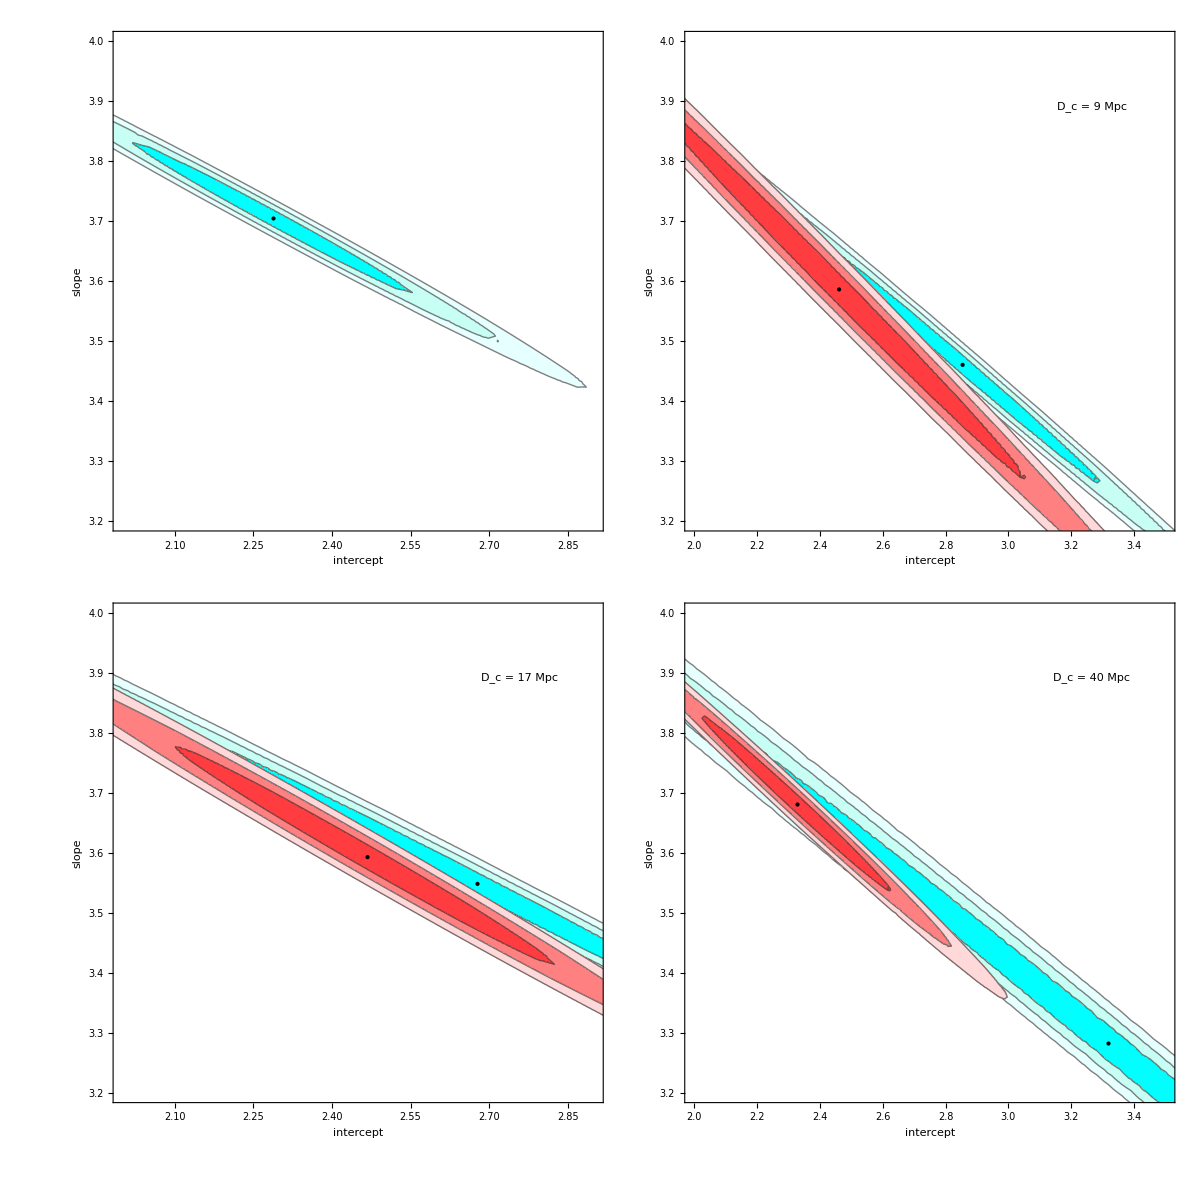

```mathematica
fig2=GraphicsGrid[{{pl1,pl2},{pl3,pl4}},Spacings->-52,ImageSize->1200]
```

```mathematica
Export[NotebookDirectory[]<>"fig2.pdf",fig2,ImageResolution->1000];
```

## Figure 1

```mathematica
sint=0.1;
tabdssd={};
tabbfic={};
Do[
tests=Select[test1,#[[1]]<dsplt &];
testl=Select[test1,#[[1]]>dsplt &];

chi2tfs[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  tests[[i,4]]^2+tests[[i,6]]^2+sint^2](tests[[i,5]]-ic-sl tests[[i,3]]))^2,{i,1,Length[tests]}];
mintfs=FindMinimum[chi2tfs[ic,sl],{ic,2},{sl,4}];
icmins=mintfs[[2,1,2]];
slmins=mintfs[[2,2,2]];
mintfsc=mintfs[[1]];

chi2tfl[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  testl[[i,4]]^2+testl[[i,6]]^2+sint^2](testl[[i,5]]-ic-sl testl[[i,3]]))^2,{i,1,Length[testl]}];
mintfl=FindMinimum[chi2tfl[ic,sl],{ic,2},{sl,3}];
icminl=mintfl[[2,1,2]];
slminl=mintfl[[2,2,2]];
mintflc=mintfl[[1]];
dchi1=chi2tfl[icmins,slmins]-mintflc;
dchi2=chi2tfs[icminl,slminl]-mintfsc;
dchimin=Min[dchi1,dchi2];
sdistmin=FindRoot[dchimin==dchi[sdist,2],{sdist,3}][[1,2]];
AppendTo[tabbfic,{dsplt,icmins,icminl}];
AppendTo[tabdssd,{dsplt,sdistmin}],{dsplt,2,70,1}]
tabbfic
```

{{2,2.51797,2.33998},{3,0.0236658,2.32384},{4,1.85627,2.37159},{5,2.20236,2.44261},{6,2.12685,2.45528},{7,2.32415,2.57068},{8,2.38151,2.78427},{9,2.46126,2.85443},{10,2.08128,2.875},{11,2.07973,2.93159},{12,2.06435,2.93664},{13,2.08457,3.00041},{14,2.01148,2.98265},{15,2.36031,2.82846},{16,2.36889,2.78742},{17,2.46788,2.67789},{18,2.38012,3.53713},{19,2.26269,3.58191},{20,2.31665,3.025},{21,2.29763,3.01529},{22,2.34046,3.06738},{23,2.33175,3.06886},{24,2.32426,3.06954},{25,2.32426,3.06954},{26,2.32426,3.06954},{27,2.32426,3.06954},{28,2.32426,3.06954},{29,2.33191,3.13206},{30,2.35403,3.12256},{31,2.35403,3.12256},{32,2.35403,3.12256},{33,2.35403,3.12256},{34,2.35403,3.12256},{35,2.35403,3.12256},{36,2.35649,3.29606},{37,2.35649,3.25224},{38,2.34758,3.25224},{39,2.34758,3.25224},{40,2.32722,3.31823},{41,2.32722,3.31823},{42,2.32722,3.31823},{43,2.32722,3.31823},{44,2.32722,3.31823},{45,2.32722,3.31823},{46,2.32722,3.31823},{47,2.32722,3.31823},{48,2.32722,3.31823},{49,2.32722,3.31823},{50,2.32722,3.32179},{51,2.37063,3.13322},{52,2.36219,3.13734},{53,2.36219,3.13734},{54,2.36927,3.76073},{55,2.36927,3.76073},{56,2.36927,3.76073},{57,2.36927,3.76073},{58,2.34525,3.78809},{59,2.34525,3.78809},{60,2.34525,3.78809},{61,2.38889,3.43787},{62,2.38889,3.43787},{63,2.38889,3.43787},{64,2.38889,3.43787},{65,2.38783,3.62551},{66,2.36647,3.56111},{67,2.36647,3.56111},{68,2.36647,3.56111},{69,2.3492,3.55625},{70,2.36491,3.35243}}

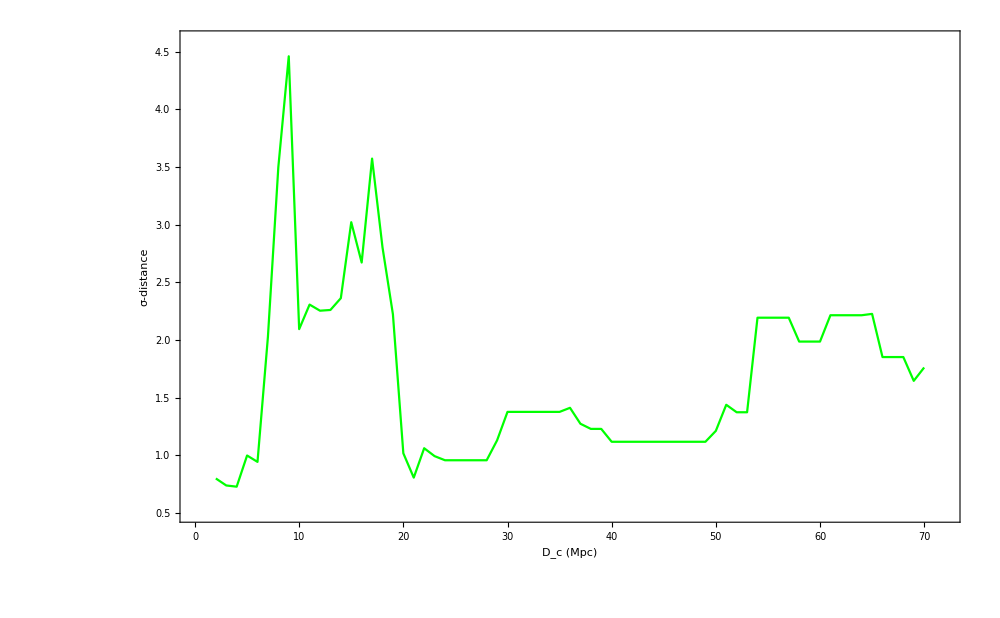

```mathematica
fig1=ListPlot[tabdssd,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{0,72},{0.5,4.6}},PlotStyle->{{Green}},ImageSize->1000, FrameStyle -> Directive[Black, Thick]]
```

```mathematica
Export[NotebookDirectory[]<>"fig1.pdf",fig1,ImageResolution->1000];
```